# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 11 - The Metropolis Monte Carlo Method

## 11.1 PRELUDE: TOSSING COINS TO COLLECT DATA

### 11.1.1 Direct simulation

```mathematica
{ RandomInteger[{0,1}],RandomInteger[{0,1}] }
```

{0,1}

```mathematica
samples={};(*empty list within which to store outcomes*)
Do[(*append new outcomes to samples list 100 times*)AppendTo[samples,{RandomInteger[{0,1}],RandomInteger[{0,1}]}];
,{100}] (*repeat Do[] loop 100 times*)
```

```mathematica
samples
```

{{1,0},{0,0},{0,0},{1,1},{1,1},{1,1},{0,0},{1,1},{1,0},{1,0},{0,0},{1,1},{0,1},{0,1},{0,0},{0,1},{1,0},{0,1},{0,0},{0,0},{0,1},{1,1},{0,1},{1,1},{0,0},{0,0},{0,0},{1,1},{0,1},{1,1},{1,0},{0,1},{0,1},{0,1},{1,1},{1,1},{0,1},{1,1},{1,1},{0,0},{1,0},{1,0},{0,1},{1,1},{1,1},{1,0},{1,1},{0,1},{0,1},{1,1},{1,0},{1,0},{0,1},{1,1},{1,1},{0,1},{0,1},{0,1},{1,1},{1,1},{0,1},{1,1},{1,0},{1,1},{0,1},{0,1},{0,1},{1,1},{0,1},{0,1},{1,0},{0,0},{1,1},{1,0},{0,0},{0,0},{1,0},{1,0},{0,1},{0,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{0,1},{0,0},{0,1},{1,1},{0,1},{1,1},{0,1},{1,1},{1,0},{1,1},{1,0},{1,0}}

```mathematica
Tally[samples]
```

{{{1,0},21},{{0,0},15},{{1,1},34},{{0,1},30}}

### 11.1.2 A random walk through configuration space

```mathematica
coins={1,0};(*heads=0,tails=1*)
samples={};(*empty list within which to store outcomes*)
Do[(*loop over coin toss trials*)
whichCoin=RandomInteger[{1,2}];(*pick a coin*)
coins[[whichCoin]]=RandomInteger[{0,1}];(*toss that coin*)
AppendTo[samples,coins];(*add new outcome to samples*)
,{100}] (*repeat Do[] loop 100 times*)

Tally[samples]
```

{{{1,1},42},{{1,0},23},{{0,0},12},{{0,1},23}}

```mathematica
Sort[Tally[samples]] (*sorted by first entry in each list item*)
```

{{{0,0},12},{{0,1},23},{{1,0},23},{{1,1},42}}

```mathematica
Tally[samples]//Sort
```

{{{0,0},12},{{0,1},23},{{1,0},23},{{1,1},42}}

```mathematica
Count[samples,{0,0}]
```

12

```mathematica
Count[samples,{0,0}]/Length[samples]
```

3/25

```mathematica
N[ Count[samples,{0,0}]/Length[samples] ]
```

0.12

### 11.1.3 A random walk through coin space

```mathematica
flip[coins_,whichCoin_]:=Module[
{newCoins=coins},(*copy the original coins list*)If[coins[[whichCoin]]==0,(*if it is currently heads...*)newCoins[[whichCoin]]=1,(*...then turn it to tails*)
newCoins[[whichCoin]]=0 (*...else turn it from tails-->heads*)
];
newCoins (*return the flipped coins list*)
]
```

```mathematica
flip[{0,0},1]
```

{1,0}

```mathematica
coins={1,0};(*heads=0, tails=1*)
samples={};(*empty list within which to store outcomes*)
Do[(*loop over coin tosses*)
whichCoin=RandomInteger[{1,2}];(*pick a coin*)
coins=flip[coins,whichCoin];(*perform the flip*) 
AppendTo[samples,coins]; (*add new outcome to samples*)
,{10000}] (*repeat Do[] loop 10,000 times*)

N[Count[samples,{0,0}]/Length[samples]]
```

0.2494

### 11.1.4 What if the probabilities are not uniform?

```mathematica
pH=0.75;
probability[coins_]:=Switch[coins,
{0,0},pH*pH,
{0,1},pH*(1-pH),
{1,0},(1-pH)*pH,
{1,1},(1-pH)*(1-pH)];
```

```mathematica
probability[{0,0}]
```

0.5625

```mathematica
coins={1,0};(*heads=0,tails=1*)
samples={};(*empty list within which to store outcomes*)
Do[(*loop over coin toss trials*)
whichCoin=RandomInteger[{1,2}];(*pick a coin*)
newCoins=flip[coins,whichCoin]; (*perform the flip and save the result*) 
If[(probability[newCoins]/probability[coins]>1),(*newCoins more likely?*)coins=newCoins,(*...then accept the coin flip*)
If[RandomReal[]≤probability[newCoins]/probability[coins],(*else*)coins=newCoins,(*change was accepted anyway*)
coins=coins (*change was rejected*)
];
];
AppendTo[samples,coins];(*add new outcome to samples*),
{10000}];(*repeat Do[] loop 10,000 times*)

N[Count[samples,{0,0}]/Length[samples]] (*compute HH probability*)
```

0.5667

## 11.2 METROPOLIS MONTE CARLO ALGORITHM

## 11.3 EXAMPLES

### 11.3.1 Average population of vibrational energies as a function of temperature

#### Partition function solution

```mathematica
energyVibDiatomic[hbarOmega_,v_]:=hbarOmega*(v+0.5)
```

```mathematica
qExact[kT_,hbarOmega_]:=N[Sum[Exp[-energyVibDiatomic[hbarOmega,v]/kT],(*summand*)
{v,0,∞}]];(*index and limits*)
```

```mathematica
exactProbResult[kT_,hbarOmega_,v_]:=N[ Exp[-energyVibDiatomic[hbarOmega,v]/kT]/qExact[kT,hbarOmega] ];
```

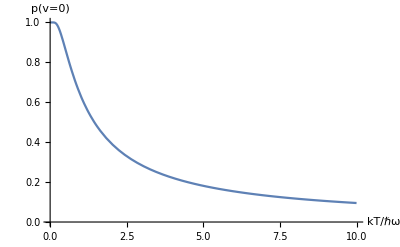

```mathematica
Plot[ exactProbResult[kT,1,0],{kT,10^-3,10},
AxesOrigin->{0,0},AxesLabel->{"kT/ℏω","p(v=0)"}]
```

```mathematica
exactProbResult[1,1,0] (*probability of v=0 when kT=1, hbarOmega=1*)
```

0.632121

#### Monte Carlo solution

```mathematica
MCstep[kT_,hbarOmega_,v_]:=Module[
{vprime,deltaE,newV},(*local variables*)
(*random±1,but keep v>0*)
vprime=Max[v+(-1)^RandomInteger[{0,1}],0];
deltaE=energyVibDiatomic[hbarOmega,vprime]-
energyVibDiatomic[hbarOmega,v];
If[deltaE≤0,
newV=vprime;,(*energy is minimized;accept change*)
If[RandomReal[]≤Exp[-deltaE/kT],(*accept with probability*)newV=vprime;,(*change was accepted*)
newV=v;(*change was rejected*)
];
];
newV (*return new value of v*)
];
```

```mathematica
v=0;hbarOmega=1;kT=1;(*define parameters*)
Do[ v=MCstep[kT,hbarOmega,v],{100}]; (*equilibrate*)
```

```mathematica
vSamples={};
Do[ (*loop over steps*)
v=MCstep[kT,hbarOmega,v];(*perform step*)
If[Mod[i,100]==0,(*is step count i a multiple of 100?...*)AppendTo[vSamples,v]];(*...then collect data*),
{i,10000}];
```

```mathematica
Tally[vSamples]//Sort
```

{{0,58},{1,26},{2,6},{3,5},{4,5}}

```mathematica
N[Count[vSamples,0]/Length[vSamples]]
```

0.58

```mathematica
runMC[kT_,hbarOmega_,nEquil_,nDataCol_]:=Module[
{v=0,vSamples={}},(*initialize local variables*)Do[v=MCstep[kT,hbarOmega,v];,{nEquil}];(*equilibration*)
Do[(*data collection*)
v=MCstep[kT,hbarOmega,v];If[Mod[i,100]==0,AppendTo[vSamples,v]];
,{i,nDataCol}];
vSamples (*return samples to be analyzed*)
];

MCProbResult[vSamples_,vTarget_]:=
N[Count[vSamples,vTarget]/Length[vSamples]]
```

```mathematica
kT=1;hbarOmega=1;
convergenceTest=Table[
{nDataCol,MCProbResult[runMC[kT,hbarOmega,100,nDataCol],0]},{nDataCol,1000,100000,2000}]
```

{{1000,0.5},{3000,0.566667},{5000,0.72},{7000,0.542857},{9000,0.6},{11000,0.645455},{13000,0.669231},{15000,0.56},{17000,0.547059},{19000,0.557895},{21000,0.709524},{23000,0.673913},{25000,0.64},{27000,0.625926},{29000,0.662069},{31000,0.612903},{33000,0.657576},{35000,0.582857},{37000,0.651351},{39000,0.664103},{41000,0.614634},{43000,0.655814},{45000,0.622222},{47000,0.631915},{49000,0.614286},{51000,0.652941},{53000,0.662264},{55000,0.625455},{57000,0.607018},{59000,0.608475},{61000,0.659016},{63000,0.631746},{65000,0.655385},{67000,0.638806},{69000,0.597101},{71000,0.639437},{73000,0.638356},{75000,0.610667},{77000,0.651948},{79000,0.627848},{81000,0.635802},{83000,0.610843},{85000,0.64},{87000,0.650575},{89000,0.619101},{91000,0.635165},{93000,0.633333},{95000,0.62},{97000,0.631959},{99000,0.59798}}

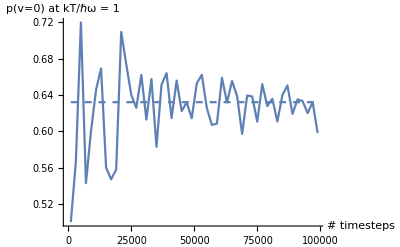

```mathematica
Show[
ListPlot[convergenceTest,Joined->True,AxesLabel->{"# timesteps","p(v=0) at kT/ℏω = 1"}],Plot[exactProbResult[1,1,0],{x,1000,99000},PlotStyle->Dashed]]
```

### 11.3.2 Vibrational heat capacity

#### Partition function solution

```mathematica
avgE[hbarOmega_,kT_]:=N[Sum[
energyVibDiatomic[hbarOmega,v]*Exp[-energyVibDiatomic[hbarOmega,v]/kT],{v,0,∞}]/qExact[kT,hbarOmega]];
```

```mathematica
dh=10^-3;(*define the step size*)
(avgE[1,1+dh]-avgE[1,1])/dh (*calculate forward difference*)
```

0.920749

```mathematica
(avgE[1,1]-avgE[1,1-dh])/dh (*reverse difference,previously defined dh*)
```

0.920598

```mathematica
(avgE[1,1+dh/2]-avgE[1,1-dh/2])/dh (*central difference,prev.def.dh*)
```

0.920674

```mathematica
avgE2[hbarOmega_,kT_]:=N[Sum[
energyVibDiatomic[hbarOmega,v]^2*Exp[-energyVibDiatomic[hbarOmega,v]/kT],{v,0,∞}]/qExact[kT,hbarOmega]];
```

```mathematica
(avgE2[1,1]-avgE[1,1]^2)/1^2 (*via standard deviation*)
```

0.920674

```mathematica
dh=10^-3;heatCapacityExactFiniteDiff[hbarOmega_,kT_]:=(avgE[hbarOmega,kT+dh/2]-avgE[hbarOmega,kT-dh/2])/dh;

heatCapacityExactStdDev[hbarOmega_,kT_]:=(avgE2[hbarOmega,kT]-avgE[hbarOmega,kT]^2)/kT^2;
```

#### Monte Carlo solution

```mathematica
runMCv2[kT_,hbarOmega_,nEquil_,nDataCol_]:=Module[
{v=0,ESamples={},E2Samples={}},(*initialize local variables*)
Do[v=MCstep[kT,hbarOmega,v];,{nEquil}];(*equilibration*)
Do[ (*data collection*)
v=MCstep[kT,hbarOmega,v];
If[Mod[i,100]==0,(*collect data every 100 steps*)AppendTo[ESamples,energyVibDiatomic[hbarOmega,v]];
AppendTo[E2Samples,(energyVibDiatomic[hbarOmega,v])^2];
];
,{i,nDataCol}];
{ESamples,E2Samples} (*return samples to be analyzed*)
];

kT=1;hbarOmega=1;
{ESamples,E2Samples}=runMCv2[kT,hbarOmega,100,50000];
```

```mathematica
heatCapacityFromSamples[ESamples_,E2Samples_,kT_]:=(Mean[E2Samples]-(Mean[ESamples])^2)/kT^2
```

```mathematica
heatCapacityFromSamplesVariance[ESamples_,kT_]:=Variance[ESamples]/kT^2
```

```mathematica
heatCapacityExactStdDev[hbarOmega,kT]
heatCapacityFromSamples[ESamples,E2Samples,kT]
heatCapacityFromSamplesVariance[ESamples,kT]
```

0.920674

0.882124

0.883892